Hamiltonian of monolayer MoS2
	Reproduce the work of Andor for monolayer MoS2 k·p Hamiltonian:

With no SOC:

```mathematica
ClearAll["Global`*"]
```

```mathematica
Clear["`*"]
```

```mathematica
Hkp=({{Subscript[ϵ, v], Subscript[ℽ, 3]*SubMinus[q], Subscript[ℽ, 2]*SubPlus[q], Subscript[ℽ, 4]*SubPlus[q]}, {Subscript[ℽ, 3]*SubMinus[q], Subscript[ϵ, c], Subscript[ℽ, 5]*SubMinus[q], Subscript[ℽ, 6]*SubMinus[q]}, {Subscript[ℽ, 2]*SubPlus[q], Subscript[ℽ, 5]*SubMinus[q], Subscript[ϵ, v-3], 0}, {Subscript[ℽ, 4]*SubPlus[q], Subscript[ℽ, 6]*SubMinus[q], 0, Subscript[ϵ, c+2]}})
```

{{ϵ_v,q_- ℽ_3,q_+ ℽ_2,q_+ ℽ_4},{q_- ℽ_3,ϵ_c,q_- ℽ_5,q_- ℽ_6},{q_+ ℽ_2,q_- ℽ_5,ϵ_(-3+v),0},{q_+ ℽ_4,q_- ℽ_6,0,ϵ_(2+c)}}

Settings for K points for now:

```mathematica
SubPlus[q]= Subscript[q, x]+ⅈ*Subscript[q, y]
```

q_x+ⅈ q_y

```mathematica
SubMinus[q]= Subscript[q, x]-ⅈ*Subscript[q, y]
```

q_x-ⅈ q_y

```mathematica
τ=1
```

1

```mathematica
Heff=H0+Has+H3w+Hcub
```

H0+H3w+Has+Hcub

```mathematica
H0 = ({{Subscript[ϵ, v], τ*Subscript[ℽ, 3]*SubMinus[q]}, {τ*Subscript[ℽ, 3]*SubPlus[q], Subscript[ϵ, c]}})
```

{{ϵ_v,(q_x-ⅈ q_y) ℽ_3},{(q_x+ⅈ q_y) ℽ_3,ϵ_c}}

```mathematica
Has = ({{α*(Subscript[q, x]*Subscript[q, x]+Subscript[q, y]*Subscript[q, y]), 0}, {0, β*(Subscript[q, x]*Subscript[q, x]+Subscript[q, y]*Subscript[q, y])}})
```

{{α (q_x^2+q_y^2),0},{0,β (q_x^2+q_y^2)}}

```mathematica
H0+Has
```

{{α (q_x^2+q_y^2)+ϵ_v,(q_x-ⅈ q_y) ℽ_3},{(q_x+ⅈ q_y) ℽ_3,β (q_x^2+q_y^2)+ϵ_c}}

```mathematica
H3w = ({{0, (SubPlus[q])^2}, {(SubMinus[q])^2, 0}})*κ
```

{{0,κ (q_x+ⅈ q_y)^2},{κ (q_x-ⅈ q_y)^2,0}}

```mathematica
τ = 1
```

1

```mathematica
Hcub= -τ*η/2*(Subscript[q, x]^2+Subscript[q, y]^2)*({{0, SubMinus[q]}, {SubPlus[q], 0}})
```

{{0,-1/2 η (q_x-ⅈ q_y) (q_x^2+q_y^2)},{-1/2 η (q_x+ⅈ q_y) (q_x^2+q_y^2),0}}

```mathematica
H=H0+Has+H3w+Hcub
```

{{α (q_x^2+q_y^2)+ϵ_v,κ (q_x+ⅈ q_y)^2-1/2 η (q_x-ⅈ q_y) (q_x^2+q_y^2)+(q_x-ⅈ q_y) ℽ_3},{κ (q_x-ⅈ q_y)^2-1/2 η (q_x+ⅈ q_y) (q_x^2+q_y^2)+(q_x+ⅈ q_y) ℽ_3,β (q_x^2+q_y^2)+ϵ_c}}

```mathematica
α = 1.73
```

1.73

```mathematica
β = -0.13
```

-0.13

```mathematica
η = 8.53
```

8.53

```mathematica
Subscript[ℽ, 3] = 3.82
```

3.82

```mathematica
κ  = -1.02
```

-1.02

```mathematica
H
```

{{1.73 (q_x^2+q_y^2)+ϵ_v,3.82 (q_x-ⅈ q_y)-1.02 (q_x+ⅈ q_y)^2-4.265 (q_x-ⅈ q_y) (q_x^2+q_y^2)},{-1.02 (q_x-ⅈ q_y)^2+3.82 (q_x+ⅈ q_y)-4.265 (q_x+ⅈ q_y) (q_x^2+q_y^2),-0.13 (q_x^2+q_y^2)+ϵ_c}}

```mathematica
? Manipulate
```

RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a version of StyleBox["expr", "TI"] with controls added to allow interactive manipulation of the value of StyleBox["u", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["du", "TI"]}], "}"}]}], "]"}] allows the value of StyleBox["u", "TI"] to vary between SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]] in steps StyleBox["du", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]}], "}"}], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] takes the initial value of StyleBox["u", "TI"] to be SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] labels the controls for StyleBox["u", "TI"] with SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] allows StyleBox["u", "TI"] to take on discrete values RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] provides controls to manipulate each of the RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["u", "TI"]], "->", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["v", "TI"]], "->", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "]"}] links the controls to the specified controllers on an external device.

```mathematica
Subscript[ϵ, v] = -0.8
```

-0.8

```mathematica
Subscript[ϵ, c] = 1.0
```

1.

```mathematica
H
```

{{-0.8+1.73 (q_x^2+q_y^2),3.82 (q_x-ⅈ q_y)-1.02 (q_x+ⅈ q_y)^2-4.265 (q_x-ⅈ q_y) (q_x^2+q_y^2)},{-1.02 (q_x-ⅈ q_y)^2+3.82 (q_x+ⅈ q_y)-4.265 (q_x+ⅈ q_y) (q_x^2+q_y^2),1.-0.13 (q_x^2+q_y^2)}}

```mathematica
Eigenvalues[H]
```

{0.5 (0.2+1.6 q_x^2+1.6 q_y^2-√(3.24+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6-(0.+1.42109×10^-14 ⅈ) q_x^3 q_y+51.6736 q_y^2+93.5136 q_x q_y^2-245.434 q_x^2 q_y^2-69.6048 q_x^3 q_y^2+218.283 q_x^4 q_y^2-122.717 q_y^4-104.407 q_x q_y^4+218.283 q_x^2 q_y^4+72.7609 q_y^6)),0.5 (0.2+1.6 q_x^2+1.6 q_y^2+√(3.24+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6-(0.+1.42109×10^-14 ⅈ) q_x^3 q_y+51.6736 q_y^2+93.5136 q_x q_y^2-245.434 q_x^2 q_y^2-69.6048 q_x^3 q_y^2+218.283 q_x^4 q_y^2-122.717 q_y^4-104.407 q_x q_y^4+218.283 q_x^2 q_y^4+72.7609 q_y^6))}

```mathematica
ConjugateTranspose[H]
```

{{-0.8+1.73 (Conjugate[q_x]^2+Conjugate[q_y]^2),Conjugate[-1.02 (q_x-ⅈ q_y)^2+3.82 (q_x+ⅈ q_y)-4.265 (q_x+ⅈ q_y) (q_x^2+q_y^2)]},{Conjugate[3.82 (q_x-ⅈ q_y)-1.02 (q_x+ⅈ q_y)^2-4.265 (q_x-ⅈ q_y) (q_x^2+q_y^2)],1.-0.13 (Conjugate[q_x]^2+Conjugate[q_y]^2)}}

```mathematica
Ebands = Eigenvalues[H]
```

{0.5 (0.2+1.6 q_x^2+1.6 q_y^2-√(3.24+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6-(0.+1.42109×10^-14 ⅈ) q_x^3 q_y+51.6736 q_y^2+93.5136 q_x q_y^2-245.434 q_x^2 q_y^2-69.6048 q_x^3 q_y^2+218.283 q_x^4 q_y^2-122.717 q_y^4-104.407 q_x q_y^4+218.283 q_x^2 q_y^4+72.7609 q_y^6)),0.5 (0.2+1.6 q_x^2+1.6 q_y^2+√(3.24+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6-(0.+1.42109×10^-14 ⅈ) q_x^3 q_y+51.6736 q_y^2+93.5136 q_x q_y^2-245.434 q_x^2 q_y^2-69.6048 q_x^3 q_y^2+218.283 q_x^4 q_y^2-122.717 q_y^4-104.407 q_x q_y^4+218.283 q_x^2 q_y^4+72.7609 q_y^6))}

```mathematica
Plot3D[Ebands,{Subscript[q, x],-0.2,0.2},{Subscript[q, y],-0.2,0.2}]
```

-Graphics3D-

```mathematica
Subscript[q, y]=0
```

0

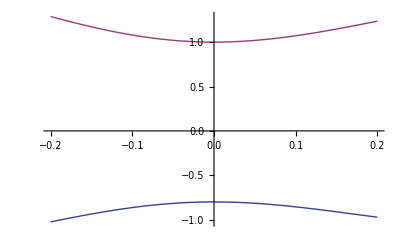

```mathematica
Plot[Ebands,{Subscript[q, x],-0.2,0.2}]
```

```mathematica
?Derivative
```

f' represents the derivative of a function f of one argument. 
Derivative[n_1,n_2,…][f] is the general form, representing a function obtained from f by differentiating n_1 times with respect to the first argument, n_2 times with respect to the second argument, and so on.

```mathematica
effmass = D[Ebands,{Subscript[q, x],2}]
```

{0.5 (3.2+((103.347 q_x-93.5136 q_x^2-490.869 q_x^3+174.012 q_x^4+436.565 q_x^5)^2)/(4 ((3.24+0. ⅈ)+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6)^(3/2))-(103.347-187.027 q_x-1472.61 q_x^2+696.048 q_x^3+2182.83 q_x^4)/(2 √((3.24+0. ⅈ)+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6))),0.5 (3.2-((103.347 q_x-93.5136 q_x^2-490.869 q_x^3+174.012 q_x^4+436.565 q_x^5)^2)/(4 ((3.24+0. ⅈ)+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6)^(3/2))+(103.347-187.027 q_x-1472.61 q_x^2+696.048 q_x^3+2182.83 q_x^4)/(2 √((3.24+0. ⅈ)+51.6736 q_x^2-31.1712 q_x^3-122.717 q_x^4+34.8024 q_x^5+72.7609 q_x^6)))}

```mathematica
Subscript[q, x] = 0
```

0

```mathematica
effmass
```

{-12.7538+0. ⅈ,15.9538+0. ⅈ}

For Gamma Point: 
the dispersion is isotropic and can be discribed by parabolic Hamiltonian:

```mathematica
effmass_gamma =-3.65
```

-3.65

```mathematica
H =( Subscript[k, x]^2+Subscript[k, y]^2)/(2*(-3.65))
```

-0.136986 (k_x^2+k_y^2)

```mathematica
Plot3D[H,{Subscript[k, x],-0.1,0.1},{Subscript[k, y],-0.1,0.1}]
```

-Graphics3D-

```mathematica
Subscript[k, y] = 0
```

0

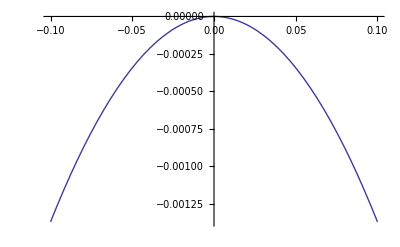

```mathematica
Plot[H,{Subscript[k, x],-0.1,0.1}]
```